# IGraph/M

## use igraph from Mathematica

This notebook can (and should) be opened using the command IGDocumentation[]. When opened like this, it cannot be saved, so feel free to re-evaluate cells and experiment.

The documentation is currently incompete. Contributions are welcome!

## Basic usage

The package can be loaded using

```mathematica
<<IGraphM`
```

The list of included functions is below. Notice that their names always have the IG prefix. Click on the name of a function to see its usage message.

```mathematica
?IGraphM`*
```

Or just type a question mark followed by the symbol’s name:

```mathematica
?IGVersion
```

IGVersion[] returns the version of the igraph library in use.

```mathematica
IGVersion[]
```

IGraph/M 0.1.2
igraph 0.8.0-pre+1f7c4ea (Sep 14 2015)
Mac OS X x86 (64-bit)

IGraph/M functions work directly with Mathematica’s builtin Graph datatype. No new special graph datatype is introduced.

Let’s take a look at a few examples. Let us first generate a graph using the builtin functions of Mathematica.

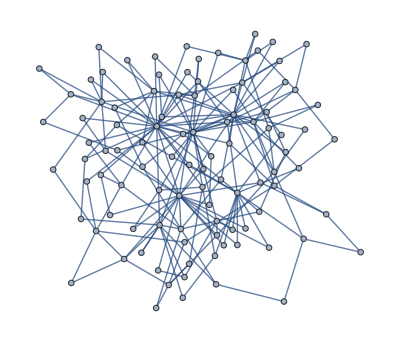

```mathematica
g=RandomGraph[BarabasiAlbertGraphDistribution[100,2]]
```

We can compute the betweenness centrality of each vertex using IGraph/M ...

```mathematica
IGBetweenness[g]
```

{754.483,893.866,113.62,1493.23,173.262,1119.18,153.798,201.321,304.579,9.61681,419.458,85.3156,515.571,145.358,107.384,54.4019,84.6173,119.058,243.524,172.064,162.206,90.2656,138.857,106.519,25.0373,15.4652,7.20996,273.462,72.8325,0.,46.2336,209.295,18.0242,127.774,99.1719,6.58294,9.61357,18.0013,51.6138,38.9812,58.9631,44.0341,61.6898,27.9393,23.631,0.,44.1685,15.1997,11.287,0.,0.,11.679,58.3969,11.9975,9.6759,30.5533,30.7791,8.28333,43.0564,0.,38.4125,40.9778,7.36508,7.33146,29.1082,0.,7.33146,0.,45.5235,6.95765,16.4413,9.49722,12.3641,48.9398,21.8979,53.3401,11.287,9.31667,9.0373,10.4631,7.80675,14.0363,3.03333,7.97302,11.287,16.0532,11.0512,11.9028,13.7694,6.58333,10.344,18.5286,7.56111,9.97424,16.2242,10.104,11.287,15.841,0.,8.86353}

... or using Mathematica, and obtain the same result.

```mathematica
BetweennessCentrality[g]
```

{754.483,893.866,113.62,1493.23,173.262,1119.18,153.798,201.321,304.579,9.61681,419.458,85.3156,515.571,145.358,107.384,54.4019,84.6173,119.058,243.524,172.064,162.206,90.2656,138.857,106.519,25.0373,15.4652,7.20996,273.462,72.8325,0.,46.2336,209.295,18.0242,127.774,99.1719,6.58294,9.61357,18.0013,51.6138,38.9812,58.9631,44.0341,61.6898,27.9393,23.631,0.,44.1685,15.1997,11.287,0.,0.,11.679,58.3969,11.9975,9.6759,30.5533,30.7791,8.28333,43.0564,0.,38.4125,40.9778,7.36508,7.33146,29.1082,0.,7.33146,0.,45.5235,6.95765,16.4413,9.49722,12.3641,48.9398,21.8979,53.3401,11.287,9.31667,9.0373,10.4631,7.80675,14.0363,3.03333,7.97302,11.287,16.0532,11.0512,11.9028,13.7694,6.58333,10.344,18.5286,7.56111,9.97424,16.2242,10.104,11.287,15.841,0.,8.86353}

Let us now assign weights to the edges. Many IGraph/M functions, including IGBetweenness, support edge weights.

```mathematica
wg=SetProperty[g,EdgeWeight->RandomReal[1,EdgeCount[g]]];
```

```mathematica
IGBetweenness[wg]
```

{1095.,1632.,572.,2039.,142.,1102.,190.,130.,326.,0.,283.,477.,479.,431.,11.,390.,0.,286.,426.,52.,148.,135.,252.,168.,0.,0.,0.,158.,72.,0.,22.,562.,0.,94.,126.,7.,0.,460.,0.,49.,612.,118.,46.,0.,34.,0.,349.,25.,0.,0.,0.,0.,178.,103.,0.,177.,64.,0.,0.,0.,0.,0.,0.,0.,90.,403.,252.,0.,433.,0.,0.,59.,4.,0.,109.,28.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,64.,408.,0.,0.,19.,14.,69.,2.,18.,81.,0.,0.,0.,15.}

Notice that Mathematica 10.2 does not include functionality to compute weighted betweenness. BetweennessCentrality[] ignores the weights.

```mathematica
BetweennessCentrality[wg]
```

{754.483,893.866,113.62,1493.23,173.262,1119.18,153.798,201.321,304.579,9.61681,419.458,85.3156,515.571,145.358,107.384,54.4019,84.6173,119.058,243.524,172.064,162.206,90.2656,138.857,106.519,25.0373,15.4652,7.20996,273.462,72.8325,0.,46.2336,209.295,18.0242,127.774,99.1719,6.58294,9.61357,18.0013,51.6138,38.9812,58.9631,44.0341,61.6898,27.9393,23.631,0.,44.1685,15.1997,11.287,0.,0.,11.679,58.3969,11.9975,9.6759,30.5533,30.7791,8.28333,43.0564,0.,38.4125,40.9778,7.36508,7.33146,29.1082,0.,7.33146,0.,45.5235,6.95765,16.4413,9.49722,12.3641,48.9398,21.8979,53.3401,11.287,9.31667,9.0373,10.4631,7.80675,14.0363,3.03333,7.97302,11.287,16.0532,11.0512,11.9028,13.7694,6.58333,10.344,18.5286,7.56111,9.97424,16.2242,10.104,11.287,15.841,0.,8.86353}

Let us delete the minimum feedback edge set to obtain an acyclic graph:

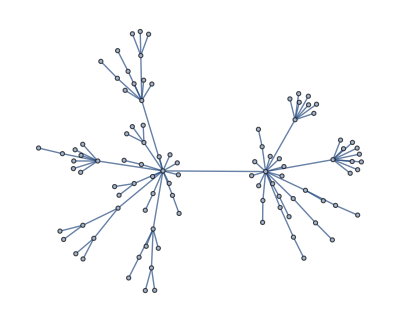

```mathematica
acg=EdgeDelete[g,IGFeedbackArcSet[g]]
```

And try out a few of igraph’s layout algorithms.

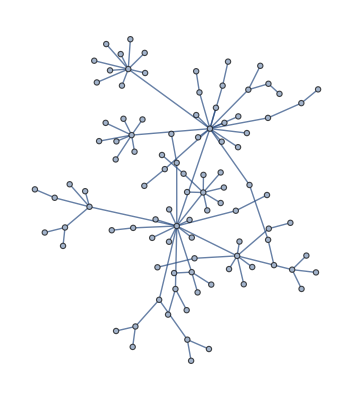
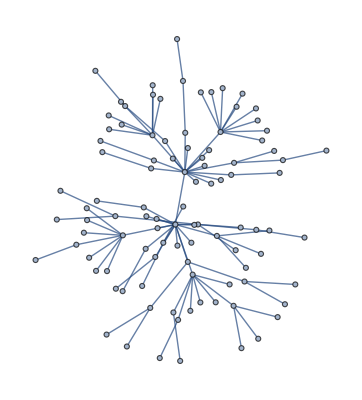
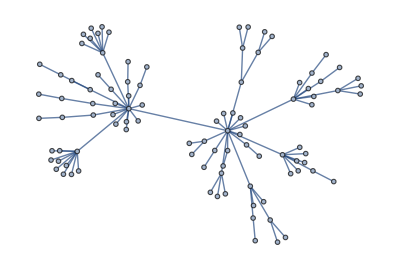

```mathematica
{IGLayoutGraphOpt[acg],IGLayoutKamadaKawai[acg],IGLayoutFruchtermanReingold[acg]}
```

Layout functions typically have many options to tune:

```mathematica
Options[IGLayoutGraphOpt]
```

{MaxIterations→500,NodeCharge→0.001,NodeMass→30,SpringLength→0,SpringConstant→1,MaxStepMovement→5,Continue→False}

Increasing the number of iterations will usually improve the result.

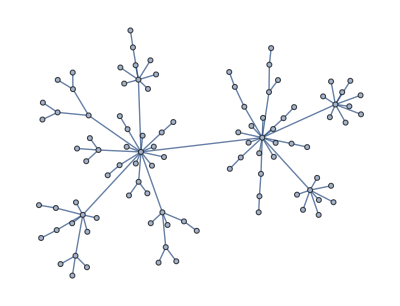

```mathematica
IGLayoutGraphOpt[acg,"MaxIterations"->5000]
```

A final note

Please refer to the usage messages for information on how to use each function. For more information on the meaning of various function options, the algorithms used by the functions, references, etc. please refer to the C/igraph documentation. The igraph documentation provides article references for most nontrivial algorithms. Note that IGraph/M is currently built using the development version of igraph (0.8.0-pre) while the online igraph documentation is for the last released version (0.7.1). Some new functionality may not yet be described in the online documentation.

The following sections provide general information on each functionality area, and show common usage patterns.

## Graph creation

All the graph creation functions in IGraph/M take any standard Mathematica Graph option such as VertexLabels, GraphStyle, VertexStyle, etc.

```mathematica
IGLCF[{-6},12,GraphStyle->"SmallNetwork"]
```

-Graphics-

Most included graph creation functions implement random graph models. These use igraph’s (not Mathematica’s) random number generator, which can be re-seeded using IGSeedRandom[].

## Structural properties

### Betwenness centrality

IGBetwenness[] and IGBetwennessEstimate[] have a "UseBigInt" option, set to True by default.

```mathematica
Options[IGBetweenness]
```

{UseBigInt→True}

Setting this to False will speed up betweenness calculation significantly but it may give incorrect results for large graphs with lots of symmetries such as GridGraph[{40,40}], due to integer overflow.

### Topological sorting and acylic graphs

IGFeedbackArcSet[] returns a set of edges the removal of which makes the graph acylic. With "Exact"→True it finds a minimal feedback arc set. With "Exact"→False it finds a feedback arc set (not necessarily minimal) using the heuristic of Eades, Lin and Smyth (1993).

## Isomorphism

igraph implements three isomorphism testing algorithms: BLISS, VF2 and LAD. These support slightly different functionality. Most of IGraph/M’s isomorphism related functions include the name of the algorithm as a prefix, e.g. IGBlissIsomorphicQ. The exceptions are IGIsomorphicQ[] and IGSubisomorphicQ[] which use igraph’s default (VF2 in the current implementation).

Functions named as …GetIsomorphism will find a single isomorphism. Functions names as …FindIsomorphisms can find multiple isomorphisms. Both return a result in a format compatible with the builtin FindGraphIsomorphism.

### BLISS

See http://www.tcs.hut.fi/Software/bliss/ and http://igraph.org/c/doc/igraph-Isomorphism.html#idm470920858320

The current implementation only supports undirected graphs.

```mathematica
?IGBliss*
```

Bliss functions take a "SplittingHeuristics" option, which can influence the performance of the method. Possible values are:

"First" – First non-unit cell. Very fast but may result in large search spaces on difficult graphs. Use for large but easy graphs.

"FirstSmallest" – First smallest non-unit cell. Fast, should usually produce smaller search spaces than "First".

"FirstLargest" – First largest non-unit cell. Fast, should usually produce smaller search spaces than "First".

"FirstMaximallyConnected" – First maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than than "First", "FirstSmallest" and "FirstLargest".

"FirstSmallestMaximallyConnected" – First smallest maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

"FirstLargestMaximallyConnected" – First largest maximally non-trivially connected non-unit cell. Not so fast, should usually produce smaller search spaces than "First", "FirstSmallest" and "FirstLargest".

Note: The result of the IGBlissCanonicalLabeling, IGBlissCanonicalPermutation and IGBlissanonicalGraph functions depend on the choice of "SplittingHeuristics". See the Bliss documentation for more information.

### VF2

```mathematica
?IGVF2*
```

VF2 supports vertex coloured and edge coloured graphs. Colours can be provided as a pair of integer lists using the "VertexColors" or "EdgeColors" options.

### LAD

See http://liris.cnrs.fr/csolnon/LAD.html and http://igraph.org/c/doc/igraph-Isomorphism.html#idm470934622128

```mathematica
?IGLAD*
```

With the "Induced"→True option LAD will search for induced subgraphs.



```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-]
```

True

```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-,"Induced"->True]
```

False

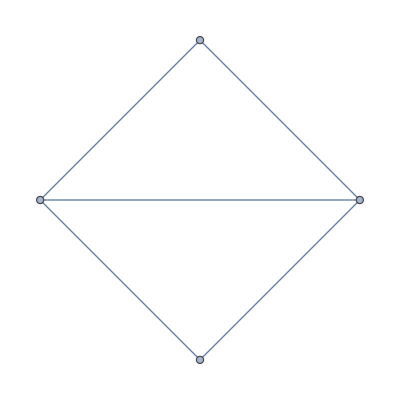
```mathematica
IGLADSubisomorphicQ[-Graphics-, -Graphics-,"Induced"->True]
```

True

## Layout algorithms

```mathematica
?IGLayout*
```

Most layout algorithms take a "MaxIterations" option. This controls either the maximum number of iterations performed by the algorithm or the exact number of iterations, depending on the specific algorithm and settings. The option name is the same for all functions to make it easier to interchange them when visualizing dynamic graphs.

Many layout algorithms can take the existing vertex coordinates as starting points. This is controlled by the "Continue" option. We can use this to visualize how the layout algorithms work …

```mathematica
g=IGLayoutRandom@RandomGraph[BarabasiAlbertGraphDistribution[100,1]];
ListAnimate@NestList[IGLayoutGraphOpt[#,"Continue"->True,"MaxIterations"->80]&,g,40]
```

… or to visualize dynamic graph processes such as adding edges to the graph one by one:

```mathematica
g=IGLayoutKamadaKawai@Graph[Range[25],{1<->25},VertexLabels->"Name"];
ListAnimate@NestList[
IGLayoutKamadaKawai[EdgeAdd[#,UndirectedEdge@@RandomSample[VertexList[#],2]],"MaxIterations"->15,"Continue"->True]&,
g,
30
]
```

## Notes on other functions

### Random number generator

igraph’s random number generator can be seeded using

```mathematica
IGSeedRandom[123]
```

### IGData[]

The IGData[] function provides access to various useful datasets. In particular, it can list small directed graphs ordered based on their IGIsoclass[], i.e. the same order motif counting functions use.

```mathematica
IGData[]
```

{{AllDirectedGraphs,3},{AllDirectedGraphs,4},MANTriadLabels}

Here’s all size 3 directed graphs.

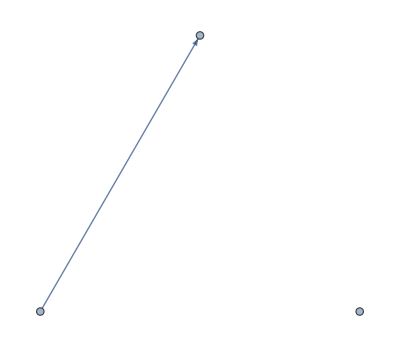
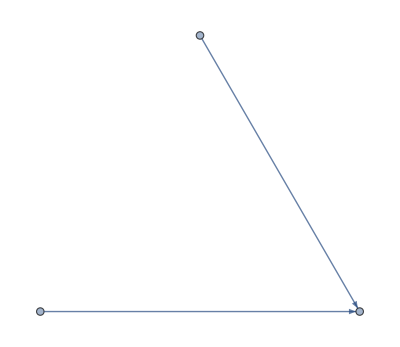
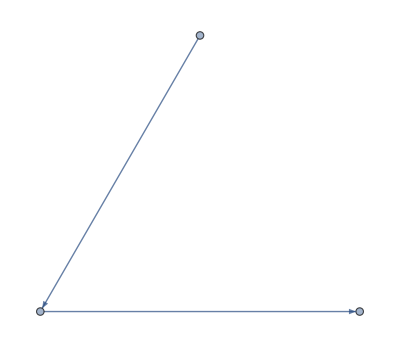
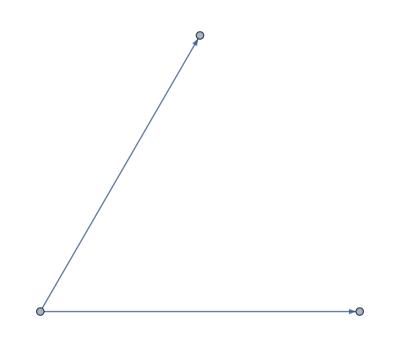
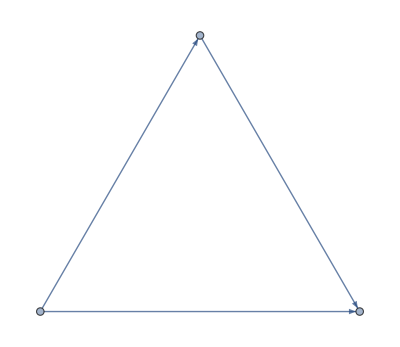
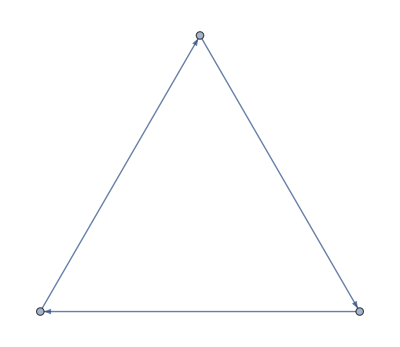
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row@IGData[{"AllDirectedGraphs",3}]
```

"MANTriadLabels" refers to the mutual, asymmetric, null labelling of triads used by IGTriadCensus[]. Each label is mapped to the corresponding graph, ordered based on their IGIsoclass. This is useful for converting the output of IGTriadCensus[] to a format compatible with IGMotifs[].